```mathematica
Clear[x,A]
```

```mathematica
a=-5/128;
b=-1/128;
y=x/6;
d=x/(3Sqrt[2]);
```

```mathematica
A[x_]={{a-x/2,0,0,0,0,0,0,0},{0,a+x/2,0,0,0,0,0,0},{0,0,a-y,0,0,-d,0,0},{0,0,0,a+y,0,0,-d,0},{0,0,0,0,b-x,0,0,0},{0,0,-d,0,0,b-2y,0,0},{0,0,0,-d,0,0,b+2y,0},{0,0,0,0,0,0,0,b+x}};
```

```mathematica
A[x]//MatrixForm
```

(-5/128-x/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -5/128+x/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -5/128-x/6 | 0 | 0 | -x/(3 √2) | 0 | 0
0 | 0 | 0 | -5/128+x/6 | 0 | 0 | -x/(3 √2) | 0
0 | 0 | 0 | 0 | -1/128-x | 0 | 0 | 0
0 | 0 | -x/(3 √2) | 0 | 0 | -1/128-x/3 | 0 | 0
0 | 0 | 0 | -x/(3 √2) | 0 | 0 | -1/128+x/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/128+x)

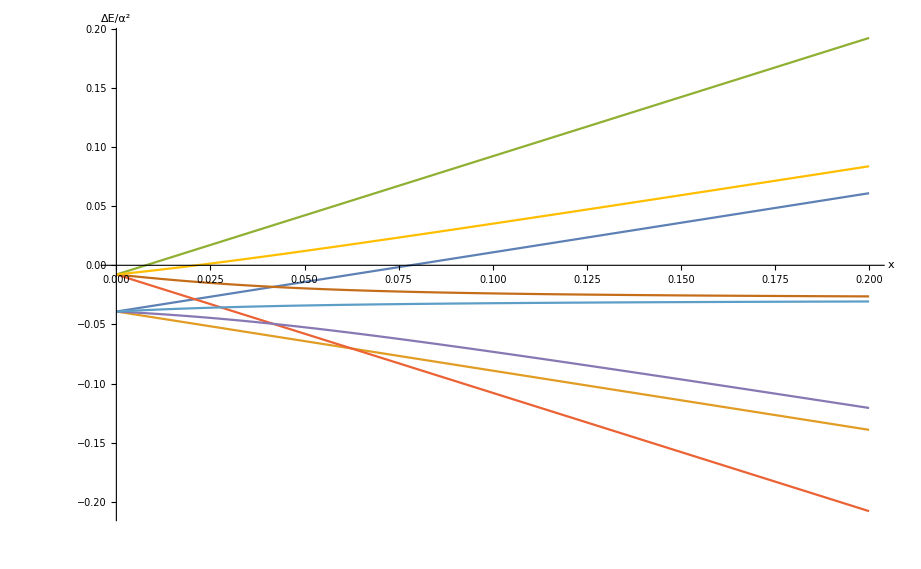

```mathematica
Plot[Evaluate[Eigenvalues[A[x]]],{x,0,0.2},AxesLabel->{x,ΔE/α^2}]
```

```mathematica
FullSimplify[Eigenvalues[A[x]],Assumptions->Element[x,Reals]]
```

{-5/128+x/2,-5/128-x/2,-1/128+x,-1/128-x,1/384 (-9-96 x-2 √(9+96 x (-1+24 x))),1/384 (-9-96 x+2 √(9+96 x (-1+24 x))),1/384 (-9+96 x-2 √(9+96 x (1+24 x))),1/384 (-9+96 x+2 √(9+96 x (1+24 x)))}

```mathematica
Eigenvectors[A[x]]
```

{{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,(3-16 x+√3 √(3-32 x+768 x^2))/(32 √2 x),0,0,1,0,0},{0,0,-(-3+16 x+√3 √(3-32 x+768 x^2))/(32 √2 x),0,0,1,0,0},{0,0,0,(3+16 x+√3 √(3+32 x+768 x^2))/(32 √2 x),0,0,1,0},{0,0,0,(3+16 x-√3 √(3+32 x+768 x^2))/(32 √2 x),0,0,1,0}}

```mathematica
Series[FullSimplify[Eigenvalues[A[x]],Assumptions->Element[x,Reals]],{x,0,1}]
```

{-5/128+x/2+O[x]^2,-5/128-x/2+O[x]^2,-1/128+x+O[x]^2,-1/128-x+O[x]^2,-5/128-x/6+O[x]^2,-1/128-x/3+O[x]^2,-5/128+x/6+O[x]^2,-1/128+x/3+O[x]^2}

```mathematica
Series[FullSimplify[Eigenvalues[A[1/x]],Assumptions->Element[x,Reals]],{x,0,1}]
```

{1/x-1/128+O[x]^2,-1/x-1/128+O[x]^2,1/(2 x)-5/128+O[x]^2,-1/(2 x)-5/128+O[x]^2,-1/(2 x)-7/384-x/2304+O[x]^2,-11/384+x/2304+O[x]^2,-11/384-x/2304+O[x]^2,1/(2 x)-7/384+x/2304+O[x]^2}